```mathematica
(*
	A function that generates a graphic of a fractal that I created in class one day.
Specify only n, which is how many iterations of the generation the code executes.
I should probably optimize the array management to make it more memory efficient
*)
```

```mathematica
GrantFractal[n_]:=Module[{i,j,k,l,pointArray,lineArray,gfxList,endPoints,endPoints2,pointArrayLength,next,del,timeArray},
pointArray={{0,0},{0,1}};
lineArray={{{0,0},{0,1}}};
endPoints={{{0,1},{{0,1},{0,1}}}};
endPoints2={};
next={};
timeArray={SessionTime[]};

For[i=1,i≤n,i++,
(*Print["i:"+i];*)
endPoints2={};
pointArrayLength=Length[pointArray];
For[j=1,j≤Length[endPoints],j++,
(*Print["Checking point"];
Print[endPoints[[j]]];*)
If[endPoints[[j,2,1]]==endPoints[[j,2,2]],
(*Print["Straight Line"];

Print["Adding Point"];
Print[{endPoints[[j,1]]+{endPoints[[j,2,1,2]],endPoints[[j,2,1,1]]},{{endPoints[[j,2,1,2]],endPoints[[j,2,1,1]]},{endPoints[[j,2,1,1]],endPoints[[j,2,1,2]]}}}];*)
AppendTo[endPoints2,{endPoints[[j,1]]+{endPoints[[j,2,1,2]],endPoints[[j,2,1,1]]},{{endPoints[[j,2,1,2]],endPoints[[j,2,1,1]]},{endPoints[[j,2,1,1]],endPoints[[j,2,1,2]]}}}];
AppendTo[lineArray,{endPoints[[j,1]],endPoints[[j,1]]+{endPoints[[j,2,1,2]],endPoints[[j,2,1,1]]}}];
AppendTo[pointArray,endPoints[[j,1]]+{endPoints[[j,2,1,2]],endPoints[[j,2,1,1]]}];


(*Print["Adding Point"];
Print[{endPoints[[j,1]]-{endPoints[[j,2,1,2]],endPoints[[j,2,1,1]]},{{-endPoints[[j,2,1,2]],-endPoints[[j,2,1,1]]},{endPoints[[j,2,1,1]],endPoints[[j,2,1,2]]}}}];*)
AppendTo[endPoints2,{endPoints[[j,1]]-{endPoints[[j,2,1,2]],endPoints[[j,2,1,1]]},{{-endPoints[[j,2,1,2]],-endPoints[[j,2,1,1]]},{endPoints[[j,2,1,1]],endPoints[[j,2,1,2]]}}}];
AppendTo[lineArray,{endPoints[[j,1]],endPoints[[j,1]]-{endPoints[[j,2,1,2]],endPoints[[j,2,1,1]]}}];
AppendTo[pointArray,endPoints[[j,1]]-{endPoints[[j,2,1,2]],endPoints[[j,2,1,1]]}];
,
(*Print["Turn"];
Print["Adding Point - Straight"];
Print[{endPoints[[j,1]]+endPoints[[j,2,1]],{endPoints[[j,2,1]],endPoints[[j,2,1]]}}];*)
AppendTo[endPoints2,{endPoints[[j,1]]+endPoints[[j,2,1]],{endPoints[[j,2,1]],endPoints[[j,2,1]]}}];
AppendTo[lineArray,{endPoints[[j,1]],endPoints[[j,1]]+endPoints[[j,2,1]]}];
AppendTo[pointArray,endPoints[[j,1]]+endPoints[[j,2,1]]];

(*Print["Adding Point - Turn"];
Print[{endPoints[[j,1]]+endPoints[[j,2,2]],{endPoints[[j,2,2]],endPoints[[j,2,1]]}}];*)
AppendTo[endPoints2,{endPoints[[j,1]]+endPoints[[j,2,2]],{endPoints[[j,2,2]],endPoints[[j,2,1]]}}];
AppendTo[lineArray,{endPoints[[j,1]],endPoints[[j,1]]+endPoints[[j,2,2]]}];
AppendTo[pointArray,endPoints[[j,1]]+endPoints[[j,2,2]]];
];
];
(*Print["endPoints2"];
Print[endPoints2];*)
endPoints={};
For[j=1,j≤Length[endPoints2],j++,
del=0;
For[k=1,k≤pointArrayLength,k++,
If[endPoints2[[j,1]]==pointArray[[k]],
del=1;
];
];
For[k=1,k≤Length[endPoints2],k++,
If[endPoints2[[j,1]]==endPoints2[[k,1]],
If[j≠k,
del=1;
];
];
];
If[del==0,
AppendTo[endPoints,endPoints2[[j]]];
];
];
(*Print[endPoints];*)
AppendTo[timeArray,SessionTime[]]
];

gfxList={Graphics[Point[pointArray]]};
For[i=1,i≤Length[lineArray],i++,
AppendTo[gfxList,Graphics[Line[lineArray[[i]]]]];
];
Show[gfxList]
(*ListPlot[timeArray-timeArray[[1]]]*)
];
```

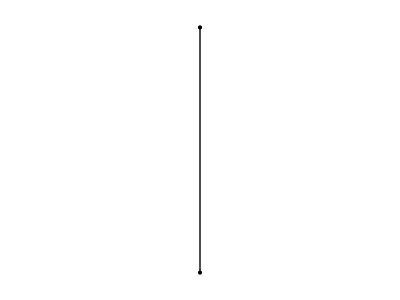

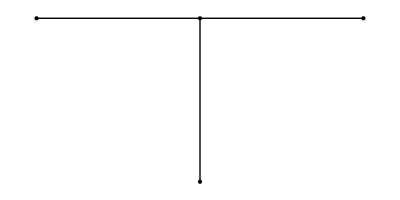

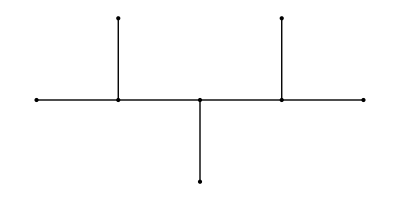

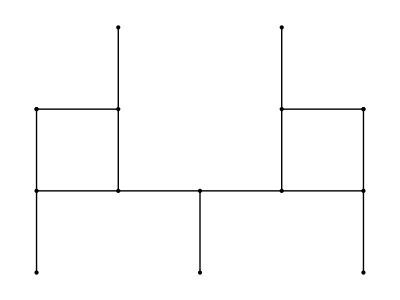

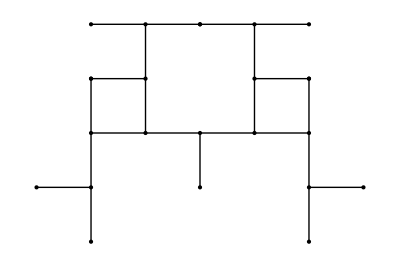

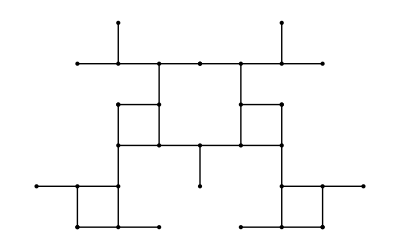

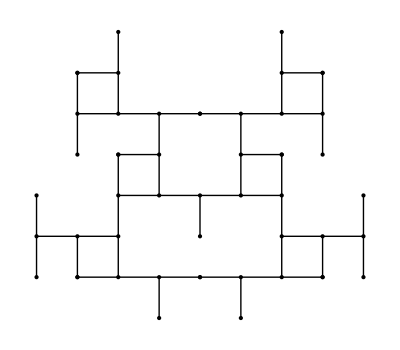

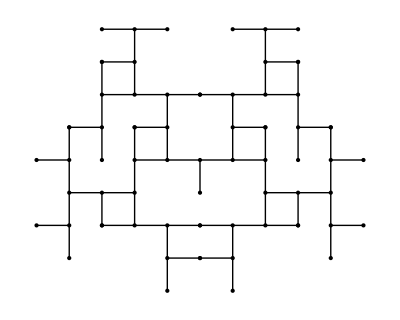

```mathematica
GrantFractal[0]
GrantFractal[1]
GrantFractal[2]
GrantFractal[3]
GrantFractal[4]
GrantFractal[5]
GrantFractal[6]
GrantFractal[7]
GrantFractal[8]
GrantFractal[9]
GrantFractal[10]
GrantFractal[11]
GrantFractal[12]
GrantFractal[13]
GrantFractal[20]
```

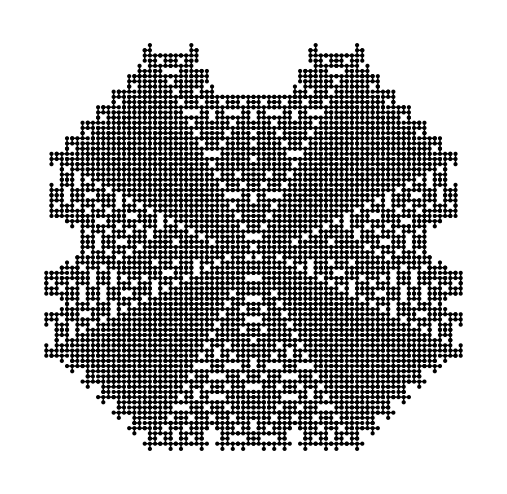

```mathematica
GrantFractal[60]
```

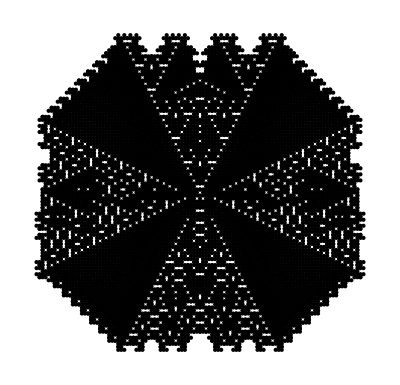

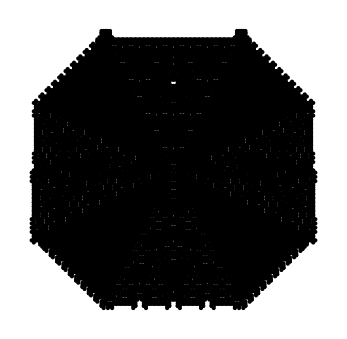

-Graphics-

```mathematica
GrantFractal[80]
GrantFractal[100]
GrantFractal[200]
GrantFractal[400]
GrantFractal[800]
```

```mathematica
GrantFractal[1000]
GrantFractal[2000]
```